# Homework assignment 9

Kyle McGraw <kmcgraw@caltech.edu>, Dallas Taylor, Sam

## Part 1: Restriction enzyme reaction schemata and systems that scramble and unscramble DNA.

(a) Examine the REschemata at the end of ReactionSchemaSimulator.nb, and based on whatever biological, chemical, or physical understanding you have, describe several aspects of the model that are unrealistic, and give examples of where specific initial state give patently crazy results.  For the types of cases you considered, describe verifiable conditions under which the crazy results would not occur.  Cases where the result isn’t really crazy, but just somewhat off, are also appreciated.  

One possible thing that the model does not account for is the ligation of sticky ends that are not perfect matches. Since the model doesn’t allow mismatches or other secondary structure, we miss out on interesting structures like hairpins and are unable to model behaviors that would arise from sticky ends that might get created that are not identical but could still be ligated together. A potential crazy result that could arise would be if we model using SmlI, AlwNI, BglI, FokI, or any RE that could generate a similar but not exact sticky end to another sticky end; this could generate a normal looking simulation that would have unexpected results in an actual experiment. For example: since BglI has a four length sticky end of anything, it could have AATC which would nearly match that of EcoRI of AATT; this would matter for any simulation but we might have to worry about it in a real experiment.

Another issue that was mentioned in the notebook is the simulation of ligases on both of the sticky ends. This prevents the simulation of inhibition due to saturation in a system. However, in an experiment we would have to be careful to have the right concentration of ligase.

(b) Scrambling with restriction enzymes.  Consider the DNA molecules called “scrambler” below, along with the simulation of the activity of EcoRI, MfeI, SalI, SmlI, and Ligase.  Observe that regardless of how many copies of the DNA are used, sufficiently long simulations will always end up in a state with DNA that can no longer be cut or ligated -- but each simulation run will result in different molecules.  Explain this phenomenon and theoretically characterize the set of molecules that can in principle arise as “terminal” molecules that cannot be cut or ligated even if additional copies of the scrambler DNA were added to the system.

EcoRI:
GAATTC        G    AATTC
CTTAAG        CTTAA    G
MfeI:
CAATTG        C    AATTG
GTTAAC        GTTAA    C
SalI:
GTCGAC        G    TCGAC
CAGCTG        CAGCT    G
SmlI:
CTCGAG        C    TCGAG
GAGCTC        GAGCT    C
SmlI (in scrambler, corresponds to SmlI):
CTCGAG        C    TCGAG
GAGCTC        GAGCT    C

In the scrambler DNA molecules, each of these enzymes cut sites appears once without overlap. Since the sticky ends of EcoRI and MfeI are the same (AATT) and the sticky ends of SalI and SmlI are the same (TCGA), we will have the EcoRI and MfeI cuts being able to ligate together as well as the SalI and SmlI cuts being able to ligate together (for both sets, a enzyme cut can ligate to either side of the same enzyme cut or either side of the corresponding enzyme cut). However, since a cut ligating to either side of the same cut (EcoRI cut to either side of EcoRI cut) will be able to be cut again (ex. EcoRI & EcoRI has GAATTC -> GAATTC), while a cut ligating to either side of the corresponding enzyme cut will not be able to be cut again (ex. EcoRI & MfeI has GAATTC -> GAATTG). Since a cut can ligate with either the top or bottom half of the corresponding cut and won’t be able to be cut at that location again, we will get different molecules each simulation but will generate terminal molecules that can’t get cut anymore.

To make your arguments clear and precise, give names A, B, C, ..., 1, 2, 3, ... to subsequences of the scrambler sequence, where A, B, C, ... are used for sequences that never appear as sticky ends, while 1, 2, 3, ... are used for sticky ends.  Let A*, ..., 1*, ... be the Watson-Crick complements of subsequences A, ..., 1, ..., e.g. if X = GATTACA then X* = TGTAATC.    Now, describe the set of possible terminal DNA molecules either as a regular expression (if you are familiar with that notation) or in terms of paths through a graph where vertices and edges may be labeled with DNA subsequences and the DNA molecule corresponding to a path has the corresponding concatenation of subsequences.

ACTGTGG    AATT    CATATGAG    TCGA    CGGCTATC    AATT    GTCTGTC    TCGA    GGAGCAT
       A                  1                 B                   2                  C                   1                 D                 2                E
                        EcoRI                               SalI                                 MfeI                               SmlI
TGACACC    TTAA    GTATACTC    AGCT    GCCGATAG    TTAA    CAGACAG    AGCT    CCTCGTA
       A*                1*               B*                   2                C*                 1*               D*               2*              E*

The X*’s are defined in the same way that they are defined in the prompt, so going right to left on the line above. Using the logic that we explained above, we can cuts at the numbered sites to get sticky ends and substitute in the either the top or bottom from the corresponding cut (both corresponding cuts are named the same number, making sure to go in the correct direction for top vs bottom). This generates the following graphs (first is tree that stops when we get one we’ve already seen, the second in the graph with the cycles). The cycles in the graph can only be taken as long as we have enough copies of the DNA.

-Graphics-

-Graphics-

```mathematica
scrambler=ToDNA["ACTGTGGAATTCATATGAGTCGACGGCTATCAATTGTCTGTCTCGAGGAGCAT"]
```

DNA[A,C,T,G,T,G,G,A,A,T,T,C,A,T,A,T,G,A,G,T,C,G,A,C,G,G,C,T,A,T,C,A,A,T,T,G,T,C,T,G,T,C,T,C,G,A,G,G,A,G,C,A,T]

```mathematica
copies=3;  (* starts to get really slow with much higher copy numbers, so rely on theory, not simulation, to make your arguments *)
Timing[history=SimulateReactionSchema[REschemata/.rates,EcoRI+MfeI+SalI+SmlI+copies Ligase+copies scrambler,10000]; Length[history]]
```

{7.26563,1495}

```mathematica
Last[Last[history]]
```

EcoRI+3 Ligase+MfeI+SalI+SmlI+DNA[A,T,G,C,T,C,C,T,C,G,A,C,G,G,C,T,A,T,C,A,A,T,T,C,C,A,C,A,G,T]+DNA[A,C,T,G,T,G,G,A,A,T,T,G,T,C,T,G,T,C,T,C,G,A,C,G,G,C,T,A,T,C,A,A,T,T,C,A,T,A,T,G,A,G,T,C,G,A,G,G,A,G,C,A,T]+DNA[A,C,T,G,T,G,G,A,A,T,T,G,T,C,T,G,T,C,T,C,G,A,C,T,C,A,T,A,T,G,A,A,T,T,G,T,C,T,G,T,C,T,C,G,A,C,T,C,A,T,A,T,G,A,A,T,T,G,A,T,A,G,C,C,G,T,C,G,A,G,G,A,G,C,A,T]

(c) Unscrambling with restriction enzymes.   This time, you will design DNA subsequences that direct restriction enzymes (along with ligase) to unscramble a four-word phrase.   Specifically, with an encoding of your choice, the enzymes will transform “don’t be happy,  worry!” into “don’t worry, be happy!”.    Your encoding will be simple: the text is to be conceptually chopped into 5 non-empty substrings of characters (including punctuation) and each of the five substrings is assigned a non-empty sequence of DNA bases.   To decode a DNA molecule, you simply find those subsequences and replace by the corresponding text, ignoring all DNA bases that aren’t a part of any of the assigned subsequences.  To encode a message, you put the subsequences together along with arbitrary “spacer” sequences that might contain special extra information.  A simulation is considered complete if it produces a single DNA molecule that is terminal, in the sense above, and which has no sticky ends. 

The code below should be sufficient; all you need to do is edit the spacers and subsequences and subtexts in the first cell immediately below, and change the enzymes if you wish.

```mathematica
(* change this section to provide your solution.  a failed attempt at a solution is shown.  *)
spacer[0]="AGGTCG";
spacer[1]="TTGCGGCCAGAATCTGTA" ;
spacer[2]="TTCGGCGAACAGCCGCTGTACGTCATAT";
spacer[3]="GGGCCCAATAGGCGA";
spacer[4]="AGCCCCCGAGGCA";
spacer[5]="CCTCCG";
(*1.5+3.5 = TTGCGGCGAATTG*)
{subseq[0],subtext[0]}={"TCGGGCGCGTTTTTA","don't "};
{subseq[1],subtext[1]}={"GGCTAGCGCTATTTATATAT","be happy"};
{subseq[2],subtext[2]}={"GCTTCGCAGTATGAAGTTCATTTAGAT",", "};
{subseq[3],subtext[3]}={"GCGTCATGTCGCACTGCGCCC","worry"};
{subseq[4],subtext[4]}={"AAAACTGTCTCTTTCCCCT","!"};
 (* your choice of all or a subset of these enzymes *)
enzymes=AlwNI+BglI+Ligase;
```

```mathematica
decode[DNA[seq___]]:= If[First[#]=="",Last[#],First[#]<>"//"<>Last[#]]&@Sort[
(StringJoin@@(#//. Table[DNA[left___,Sequence@@ToDNA[subseq[i]],right___]-> DNA[left,subtext[i],right],{i,0,4}]//.(A|T|C|G|bA|bT|bC|bG|tA|tT|tC|tG)->Sequence[]))& /@ {DNA[seq],DNA[flip[seq]]}]
```

```mathematica
initialDNA=ToDNA[spacer[0]<>subseq[0]<>spacer[1]<>subseq[1]<>spacer[2]<>subseq[2]<>spacer[3]<>subseq[3]<>spacer[4]<>subseq[4]<>spacer[5]];
decode[initialDNA]//FullForm
```

"don't be happy, worry!"

```mathematica
initialDNA
```

DNA[A,G,G,T,C,G,T,C,G,G,G,C,G,C,G,T,T,T,T,T,A,T,T,G,C,G,G,C,C,A,G,A,A,T,C,T,G,T,A,G,G,C,T,A,G,C,G,C,T,A,T,T,T,A,T,A,T,A,T,T,T,C,G,G,C,G,A,A,C,A,G,C,C,G,C,T,G,T,A,C,G,T,C,A,T,A,T,G,C,T,T,C,G,C,A,G,T,A,T,G,A,A,G,T,T,C,A,T,T,T,A,G,A,T,G,G,G,C,C,C,A,A,T,A,G,G,C,G,A,G,C,G,T,C,A,T,G,T,C,G,C,A,C,T,G,C,G,C,C,C,A,G,C,C,C,C,C,G,A,G,G,C,A,A,A,A,A,C,T,G,T,C,T,C,T,T,T,C,C,C,C,T,C,C,T,C,C,G]

```mathematica
(* you might need to make the simulation time longer or shorter for debugging and/or for ensuring the reactions go to completion *)
Timing[history=SimulateReactionSchema[REschemata/.rates,enzymes+initialDNA,10000];Length[history]]
```

{0.8125,222}

```mathematica
finalstate=Last[Last[history]];
DNAmolecules=Cases[SymbolicVariables[finalstate],_DNA];
If[Length[DNAmolecules]>1,
Print["Too many DNA molecules!"],
If[decode[First[DNAmolecules]]=="don't worry, be happy!",
Print["Congratulations!"],
Print["Doesn't look right."]]]
```

Congratulations!

```mathematica
Last[history]
```

{10063.2,AlwNI+BglI+Ligase+DNA[C,G,G,A,G,G,A,G,G,G,G,A,A,A,G,A,G,A,C,A,G,T,T,T,T,T,G,C,C,T,C,G,G,C,T,G,T,T,C,G,C,C,G,A,A,A,T,A,T,A,T,A,A,A,T,A,G,C,G,C,T,A,G,C,C,T,A,C,A,G,A,T,T,G,G,G,C,C,C,A,T,C,T,A,A,A,T,G,A,A,C,T,T,C,A,T,A,C,T,G,C,G,A,A,G,C,A,T,A,T,G,A,C,G,T,A,C,A,G,C,G,G,G,G,G,C,T,G,G,G,C,G,C,A,G,T,G,C,G,A,C,A,T,G,A,C,G,C,T,C,G,C,C,T,A,T,T,C,T,G,G,C,C,G,C,A,A,T,A,A,A,A,A,C,G,C,G,C,C,C,G,A,C,G,A,C,C,T]}

```mathematica
finalstate
```

AlwNI+BglI+Ligase+DNA[C,G,G,A,G,G,A,G,G,G,G,A,A,A,G,A,G,A,C,A,G,T,T,T,T,T,G,C,C,T,C,G,G,C,T,G,T,T,C,G,C,C,G,A,A,A,T,A,T,A,T,A,A,A,T,A,G,C,G,C,T,A,G,C,C,T,A,C,A,G,A,T,T,G,G,G,C,C,C,A,T,C,T,A,A,A,T,G,A,A,C,T,T,C,A,T,A,C,T,G,C,G,A,A,G,C,A,T,A,T,G,A,C,G,T,A,C,A,G,C,G,G,G,G,G,C,T,G,G,G,C,G,C,A,G,T,G,C,G,A,C,A,T,G,A,C,G,C,T,C,G,C,C,T,A,T,T,C,T,G,G,C,C,G,C,A,A,T,A,A,A,A,A,C,G,C,G,C,C,C,G,A,C,G,A,C,C,T]

```mathematica
DNAmolecules
```

{DNA[C,G,G,A,G,G,A,G,G,G,G,A,A,A,G,A,G,A,C,A,G,T,T,T,T,T,G,C,C,T,C,G,G,C,T,G,T,T,C,G,C,C,G,A,A,A,T,A,T,A,T,A,A,A,T,A,G,C,G,C,T,A,G,C,C,T,A,C,A,G,A,T,T,G,G,G,C,C,C,A,T,C,T,A,A,A,T,G,A,A,C,T,T,C,A,T,A,C,T,G,C,G,A,A,G,C,A,T,A,T,G,A,C,G,T,A,C,A,G,C,G,G,G,G,G,C,T,G,G,G,C,G,C,A,G,T,G,C,G,A,C,A,T,G,A,C,G,C,T,C,G,C,C,T,A,T,T,C,T,G,G,C,C,G,C,A,A,T,A,A,A,A,A,C,G,C,G,C,C,C,G,A,C,G,A,C,C,T]}

```mathematica
decode/@ DNAmolecules
```

{don't worry, be happy!}

## Part 2: Tile self-assembly

The relevant notebook is TileAssemblySimulator.nb

Your task is fairly open-ended, yet concrete: using no more than 51 tile types, design a tile system that grows from a single-tile seed to a deterministic final shape that is as large as possible.  That is, the tile system may of course have tiles added in an unknown order, thus taking different growth paths, but it must always stop when a it reaches its final shape -- and never before, and it must not be able to grow larger.   Suppose the final shape has P tiles in it (i.e. that’s how many pixels it covers).  Then by “as large as possible” I don’t mean that you must prove that there is no 51-tile-type system that grows into a larger object (indeed, it might be unprovable), but rather the spirit is, “whoever designs the tile set that makes the biggest shape wins”.  

Clearly explain the logic behind your tile system, i.e. why it works, and why it satisfies the guidelines above.

Since the busy beaver turing machine from the example notebook was able to generate a large image using few unique tiles and starting from a line of tiles seed, I decided to adapt this to try to create the largest system I could from the TM starting with a single tile. The first thing I did was create the line of tiles that the TM needed to run. Since the TM builds a rectangle out from whatever base we give it, I created the base as large as possible while staying at 51 unique tiles. Since the 3-state busy beaver turing machine uses 28 tiles while the  4-state busy beaver uses 36 but generates a longer rectangle, I tried both systems. With the 3-state busy beaver, we were able to create a base of 23 tiles, but since it only built out 22 tiles, we ended up with a rectangle of 506 total tiles. Using the 4-state busy beaver, we could only create a base of 15 tiles, but since it built out 108 tiles, we got a rectangle of 1620 total tiles. Since both the line from seed tile and TM from line are deterministic, we end up with a deterministic final shape.

```mathematica
CombSquareTileSet[L_,R_]:=Join[
Table[
Tile[NameIt[C0L],
{NameIt[0],NameIt[EW,j],Null,NameIt[EW,j-1]}/.{v_Symbol:>Null/;v===NameIt[EW,0] || v==NameIt[EW,N]},
RGBColor@@RandomReal[1,3]],
{j,L}],
{Tile[NameIt[A,0],
{NameIt[aΔ0],NameIt[EW,L+1],Null,NameIt[EW,L]}/.{v_Symbol:>Null/;v===NameIt[EW,0] || v==NameIt[EW,N]},
RGBColor@@RandomReal[1,3]]},
Table[
Tile[NameIt[C0R],
{NameIt[0],NameIt[EW,j],Null,NameIt[EW,j-1]}/.{v_Symbol:>Null/;v===NameIt[EW,0] || v==NameIt[EW,N]},
RGBColor@@RandomReal[1,3]],
{j,L+2,L+R+2}]
]
```

```mathematica
Clear[ComboG]
ComboG[Null]=0;
ComboG[v_]:=If[StringMatchQ[ToString[v],"EW*"]||StringMatchQ[ToString[v],"*Δ*"],2,1]
ComboG[x_,y_]:=If[x===y,ComboG[x],0]
```

```mathematica
CombSquareTiles=CombSquareTileSet[14,7];
CombSquareTS=TileSystem[CombSquareTiles,2,ComboG];
CombSquareSeed=SeedAssembly[{{A0}},CombSquareTiles];
```

```mathematica
SimulateAssembly[CombSquareSeed,CombSquareTS,100]
```

```mathematica
BB3={{a,0}->{b,1,+1},{b,0}->{b,1,-1},{c,0}->{c,1,-1},{a,1}->{h,1,+1},{b,1}->{c,0,+1},{c,1}->{a,1,-1}};
```

```mathematica
ComboTiles=TuringMachineTiles[BB3]~Join~CombSquareTiles;
ComboTS=TileSystem[ComboTiles,2,ComboG];
ComboSeed=SeedAssembly[{{A0}},ComboTiles]
```

```mathematica
Length[ComboTiles]
```

51

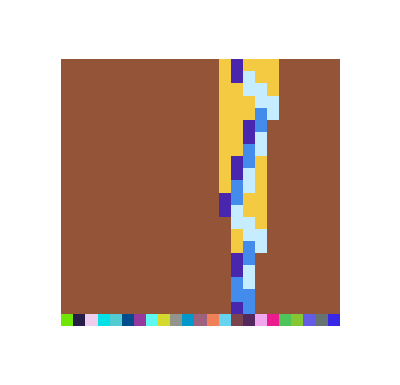

```mathematica
small=SimulateAssembly[ComboSeed,ComboTS,1000]
```

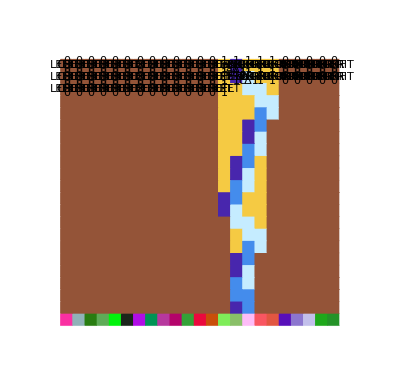

```mathematica
small//DetailForm
```

```mathematica
BB4 = {{a,0}->{b,1,+1},{b,0}->{a,1,-1},{c,0}->{h,1,+1},{d,0}->{d,1,+1},{a,1}->{b,1,-1},{b,1}->{c,0,-1},{c,1}->{d,1,-1},{d,1}->{a,0,+1}};
```

```mathematica
CombSquareTiles=CombSquareTileSet[10,3];
CombSquareTS=TileSystem[CombSquareTiles,2,ComboG];
CombSquareSeed=SeedAssembly[{{A0}},CombSquareTiles];
```

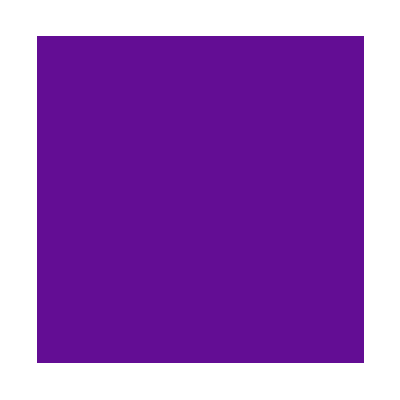

```mathematica
ComboTiles=TuringMachineTiles[BB4]~Join~CombSquareTiles;
ComboTS=TileSystem[ComboTiles,2,ComboG];
ComboSeed=SeedAssembly[{{A0}},ComboTiles]
```

```mathematica
Length[ComboTiles]
```

51

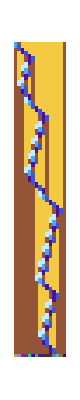

```mathematica
small=SimulateAssembly[ComboSeed,ComboTS,4000]
```

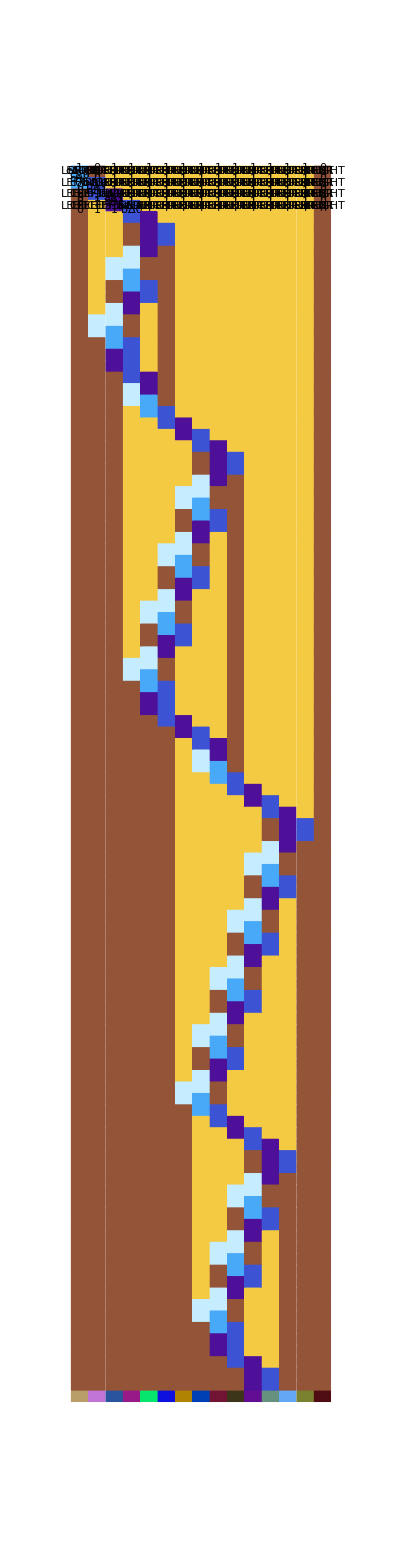

```mathematica
small//DetailForm
```

```mathematica
BB5= {{a,0}->{b,1,+1},{b,0}->{c,1,+1},{c,0}->{d,1,+1},{d,0}->{a,1,-1},{e,0}->{h,1,+1},{a,1}->{c,1,-1},{b,1}->{b,1,+1},{c,1}->{e,0,-1},{d,1}->{d,1,-1},{e,1}->{a,0,-1}};
```

```mathematica
CombSquareTiles=CombSquareTileSet[3,2];
CombSquareTS=TileSystem[CombSquareTiles,2,ComboG];
CombSquareSeed=SeedAssembly[{{A0}},CombSquareTiles];
```

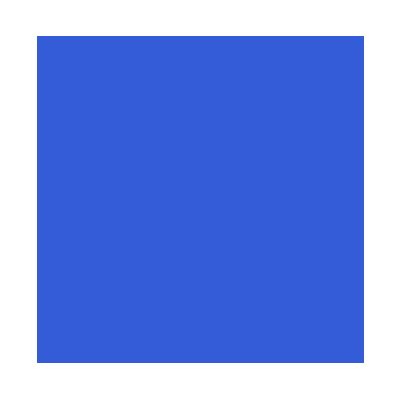

```mathematica
ComboTiles=TuringMachineTiles[BB5]~Join~CombSquareTiles;
ComboTS=TileSystem[ComboTiles,2,ComboG];
ComboSeed=SeedAssembly[{{A0}},ComboTiles]
```

```mathematica
Length[ComboTiles]
```

5

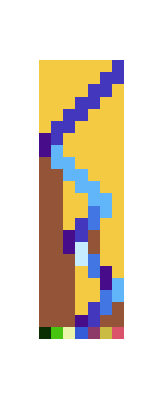

```mathematica
small=SimulateAssembly[ComboSeed,ComboTS,4000]
```

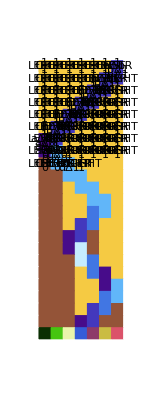

```mathematica
small//DetailForm
```